```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap3D[0.5,0.7,1.0];
sizes={32,32,32};
timeStep=0.0005;
k=-0.5;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{32,32,32} | 3 | 32768 | {7.07107,5.97614,5.} | {-7.07107,-5.97614,-5.} | {0.456198,0.385558,0.322581} | {0.430404,0.509261,0.608684} | {6.88647,8.14818,9.73894}

time | energies | moments | misc
(0) | (total | 0.981991
kinetic | 0.55
potential | 0.55
contact | -0.118009
virial | -0.354026) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 1.
sigmaY | 0.845154
sigmaZ | 0.707107
norm | 1.) | (steps | 0
A0 | 0.32524)

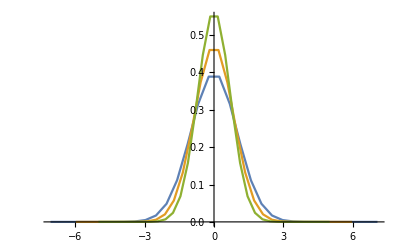

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",15,10]]
```

{177.911,Null}

time | energies | moments | misc
(15.) | (total | 0.953632
kinetic | 0.7186
potential | 0.428589
contact | -0.193557
virial | -0.000649012) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 0.83352
sigmaY | 0.740543
sigmaZ | 0.644027
norm | 1.) | (steps | 30000
A0 | 0.440458)

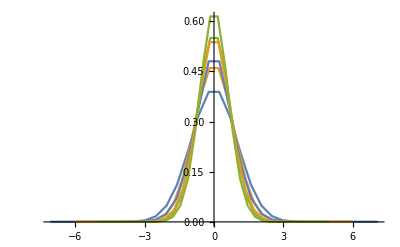

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 0.981991 | 0.55 | 0.55 | -0.118009 | -0.354026
1.5 | 0.955479 | 0.671714 | 0.455545 | -0.17178 | -0.0830015
3. | 0.953775 | 0.705685 | 0.435557 | -0.187467 | -0.0221444
4.5 | 0.953644 | 0.715038 | 0.430477 | -0.191871 | -0.00648994
6. | 0.953633 | 0.717618 | 0.429107 | -0.193092 | -0.00225226
7.5 | 0.953632 | 0.71833 | 0.428731 | -0.193429 | -0.00109004
9. | 0.953632 | 0.718526 | 0.428628 | -0.193522 | -0.000770086
10.5 | 0.953632 | 0.71858 | 0.428599 | -0.193548 | -0.000681893
12. | 0.953632 | 0.718595 | 0.428592 | -0.193555 | -0.000657571
13.5 | 0.953632 | 0.718599 | 0.428589 | -0.193557 | -0.000650862
15. | 0.953632 | 0.7186 | 0.428589 | -0.193557 | -0.000649012

```mathematica
reportMoments
```

time | meanX | meanY | meanZ | sigmaX | sigmaY | sigmaZ | norm
0 | 0 | 0 | 0 | 1. | 0.845154 | 0.707107 | 1.
1.5 | 0 | 0 | 0 | 0.883932 | 0.764789 | 0.655099 | 1.
3. | 0 | 0 | 0 | 0.847667 | 0.74661 | 0.646793 | 1.
4.5 | 0 | 0 | 0 | 0.837443 | 0.742151 | 0.644778 | 1.
6. | 0 | 0 | 0 | 0.834605 | 0.740979 | 0.644234 | 1.
7.5 | 0 | 0 | 0 | 0.833819 | 0.740662 | 0.644084 | 1.
9. | 0 | 0 | 0 | 0.833602 | 0.740576 | 0.644043 | 1.
10.5 | 0 | 0 | 0 | 0.833543 | 0.740552 | 0.644031 | 1.
12. | 0 | 0 | 0 | 0.833526 | 0.740545 | 0.644028 | 1.
13.5 | 0 | 0 | 0 | 0.833522 | 0.740543 | 0.644027 | 1.
15. | 0 | 0 | 0 | 0.83352 | 0.740543 | 0.644027 | 1.